# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[Isingnoisy];
Isingnoisy[h_,g_,J_,L_] := Module[{NNIndices,A,B,ϵ=RandomVariate[NormalDistribution[0,1],L]},
NNIndices=Normal[SparseArray[Thread[{#,#+1}->3],{L}]&/@Range[L-1]];
A=-Normal[Total[{h*Pauli[#]+g*Pauli[3#]&/@IdentityMatrix[L],J*(Pauli/@NNIndices)},2]];
B=0.001*ϵ. (Pauli/@DiagonalMatrix[ConstantArray[1,L]]);
A+B];

Clear[arrayt];
arrayt[t_,val_]:=arrayt[t,val]=Exp[-I*val*t];
Clear[new];
new[ini_,t_,La_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=ArrayReshape[N[Total[ phases*ck]],{a,a}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
Clear[purity];
purity[ini_,t_,La_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=ArrayReshape[N[Total[ phases*ck]],{a,a}];
Total[(Chop[SingularValueList[psit]])^4]
];
Clear[survival];
survival[ini_,t_,val_,vec_]:=Module[{inieigen=Conjugate[vec].ini,phases=Chop[arrayt[t,val]]*vec},
Quiet[Abs[Conjugate[ini].Total[inieigen*phases]]^2]
];

Clear[schmidt];
schmidt[ini_,t_,La_,val_,vec_]:=Module[{rho,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=N[Total[ phases*ck]];
rho=MatrixPartialTrace[Dyad[psit],2,{a,a}];
Sort[Chop[Eigenvalues[rho]]]
];
```

# Translation eigenvectors

```mathematica
L=10; (*Length of the spin chain*)
dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
```

```mathematica
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
(*Creating momentum states*)
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
(*Sorting everything*)
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
dimensions=Tally[sortedKEigen];
```

```mathematica
momentumEigenstates[[All,1]]//Sort//DeleteDuplicates
```

{0,π/5,(2 π)/5,(3 π)/5,(4 π)/5,π,(6 π)/5,(7 π)/5,(8 π)/5,(9 π)/5}

```mathematica
J=1;
h=1;
g=0.5;
H=IsingNNClosedHamiltonian[h,g,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
eigen=ParallelTable[Eigensystem[i],{i,blocks},DistributedContexts->Full];
transforms=Table[Transpose[Chop[sortedStates[[i]]]],{i,posByK}];
eigenvecs={};
Do[
a=ParallelTable[Chop[transforms[[j]].i],{i,eigen[[j,2]]},DistributedContexts->Full];
AppendTo[eigenvecs,a];
,{j,Length[transforms]}];
allvecs=Flatten[eigenvecs,1];
allvals=Flatten[Chop[eigen[[All,1]]]];
alldata=Transpose[{Chop[eigen[[All,1]]],eigenvecs}];
```

## <r>

```mathematica
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=Table[Sort[Chop[Eigenvalues[i]]],{i,blocks}];
ratios=Table[{Length[i],MeanLevelSpacingRatio[i]},{i,val}];
klist=DeleteDuplicates[ks];
```

```mathematica
ListAnimate[Table[Histogram[Differences[val[[i]]],PlotLabel->Style["dim = "<>ToString[ratios[[i,1]]]<>", k = "Text[klist[[i]]]", <r> = "<>ToString[ratios[[i,2]]],25,Black],PlotTheme->"Detailed",ImageSize->600],{i,Length[val]}],AnimationRunning->False]
```

```mathematica
glist=Range[0.01,1,0.025];
```

```mathematica
J=1;
h=1;
klist=DeleteDuplicates[ks];
```

```mathematica
alldata={};
Do[
H=IsingNNClosedHamiltonian[h,g,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=Table[Sort[Chop[Eigenvalues[i]]],{i,blocks}];
ratios=Table[{g,MeanLevelSpacingRatio[i]},{i,val}];
AppendTo[alldata,ratios];
,{g,glist}];
```

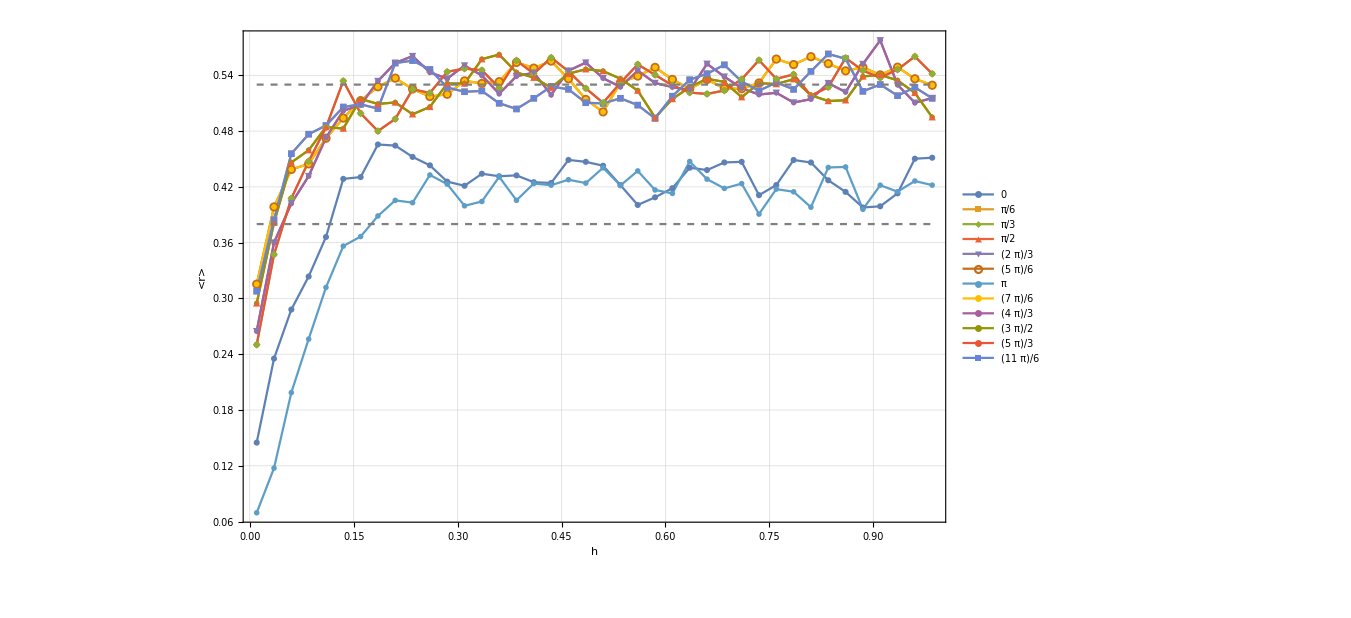

```mathematica
limits=Plot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotTheme->"Detailed",FrameLabel->{Style["h",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20]],limits,PlotRange->All,ImageSize->1000]
```

## Examples

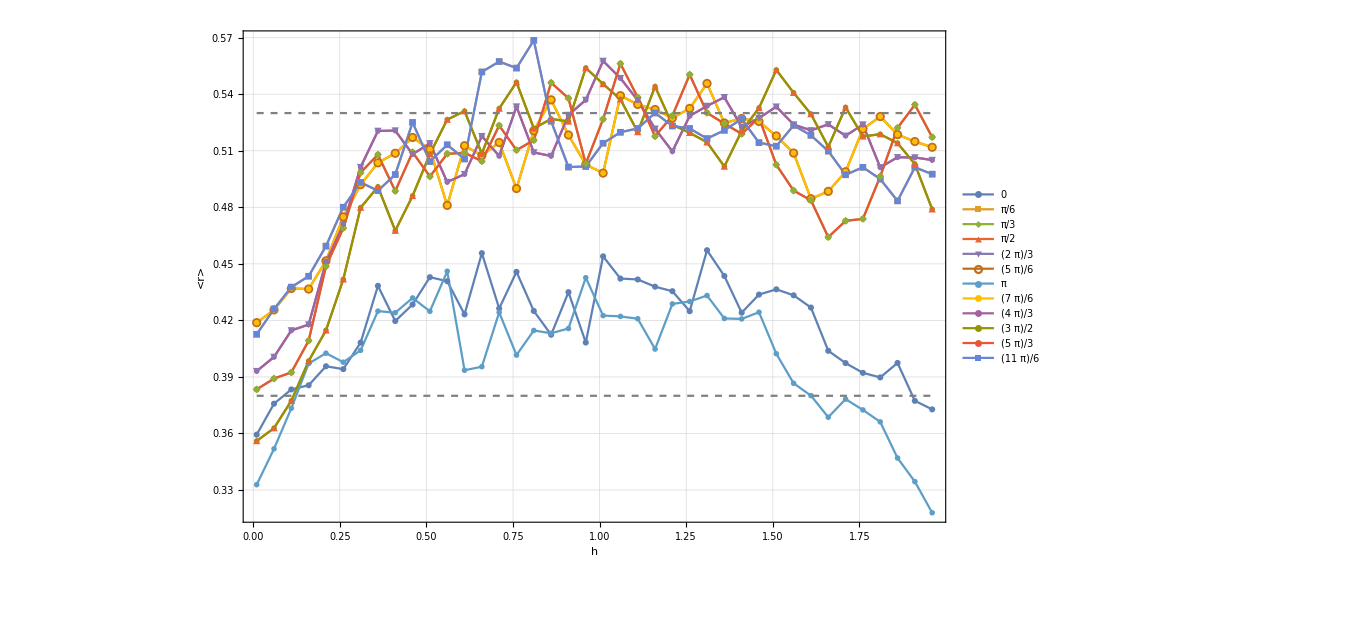

```mathematica
limits=Plot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotTheme->"Detailed",FrameLabel->{Style["h",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20]],limits,PlotRange->All,ImageSize->1000]
```

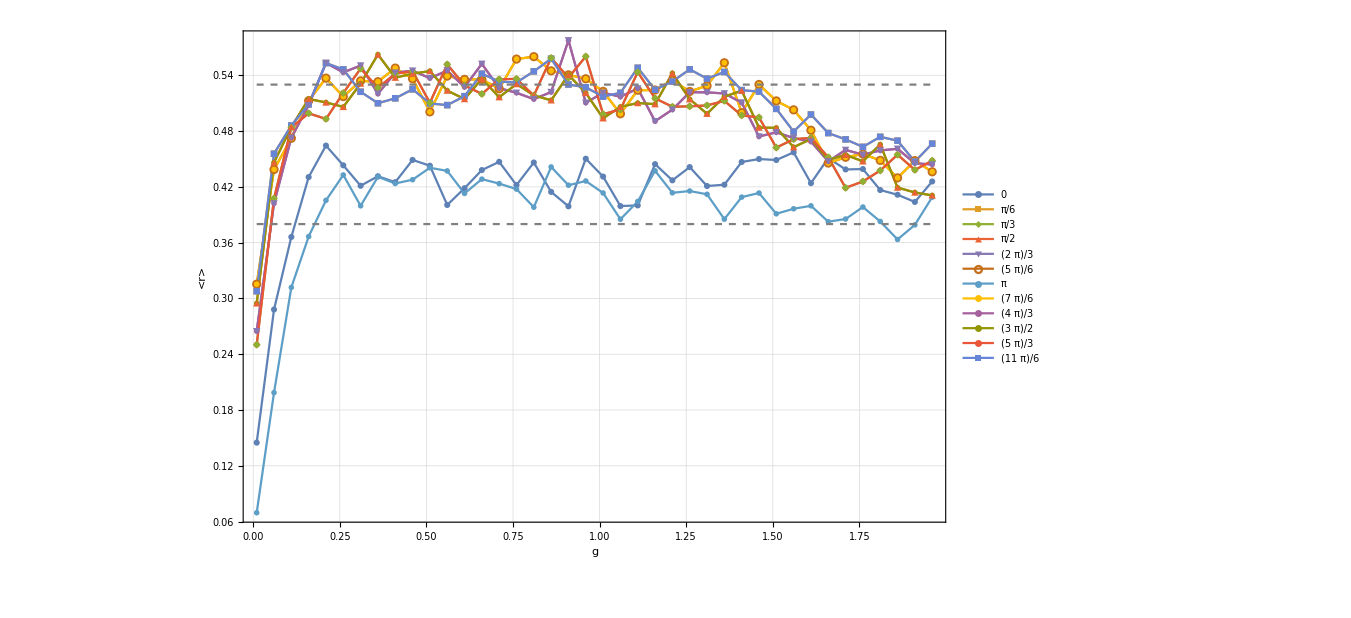

```mathematica
limits=Plot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotTheme->"Detailed",FrameLabel->{Style["g",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20]],limits,PlotRange->All,ImageSize->1000]
```

# T1

```mathematica
La=L/2;
Lb=L-La;
```

```mathematica
groups={};
Do[
d=ParallelTable[sdiag[L,La,Lb,i],{i,j[[2]]},DistributedContexts->Full];
AppendTo[groups,Transpose[{j[[1]],d}]];
,{j,alldata}];
```

```mathematica
labels=momentumEigenstates[[All,1]]//Sort//DeleteDuplicates;
```

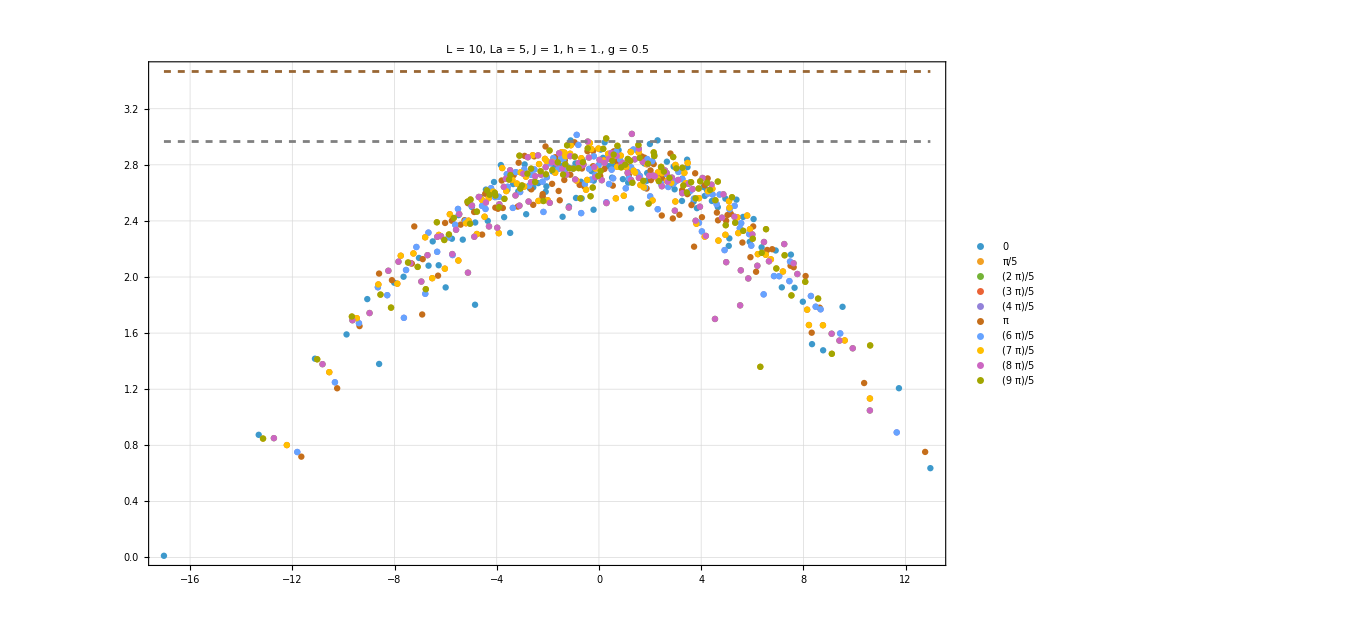

```mathematica
pbc=Show[{ListPlot[groups,PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->labels],Plot[{N[pageEntropy[L/2,L/2]],Log[2^(L/2)]},{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Dashed,Gray],Directive[Dashed,Brown]},PlotRange->All]},PlotRange->All]
```

## OBC

```mathematica
L=10;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=0.5;
h=1.;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

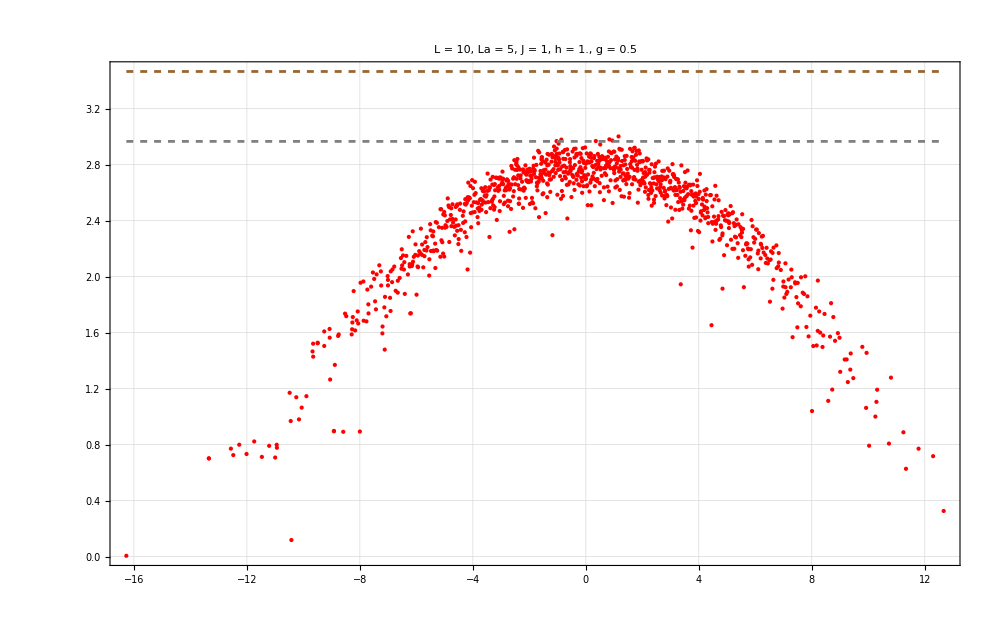

```mathematica
opc=Show[{ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Red,PointSize[0.003]],Directive[Red,PointSize[0.003]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]],Plot[{N[pageEntropy[L/2,L/2]],Log[2^(L/2)]},{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Dashed,Gray],Directive[Dashed,Brown]},PlotRange->All]},PlotRange->All]
```

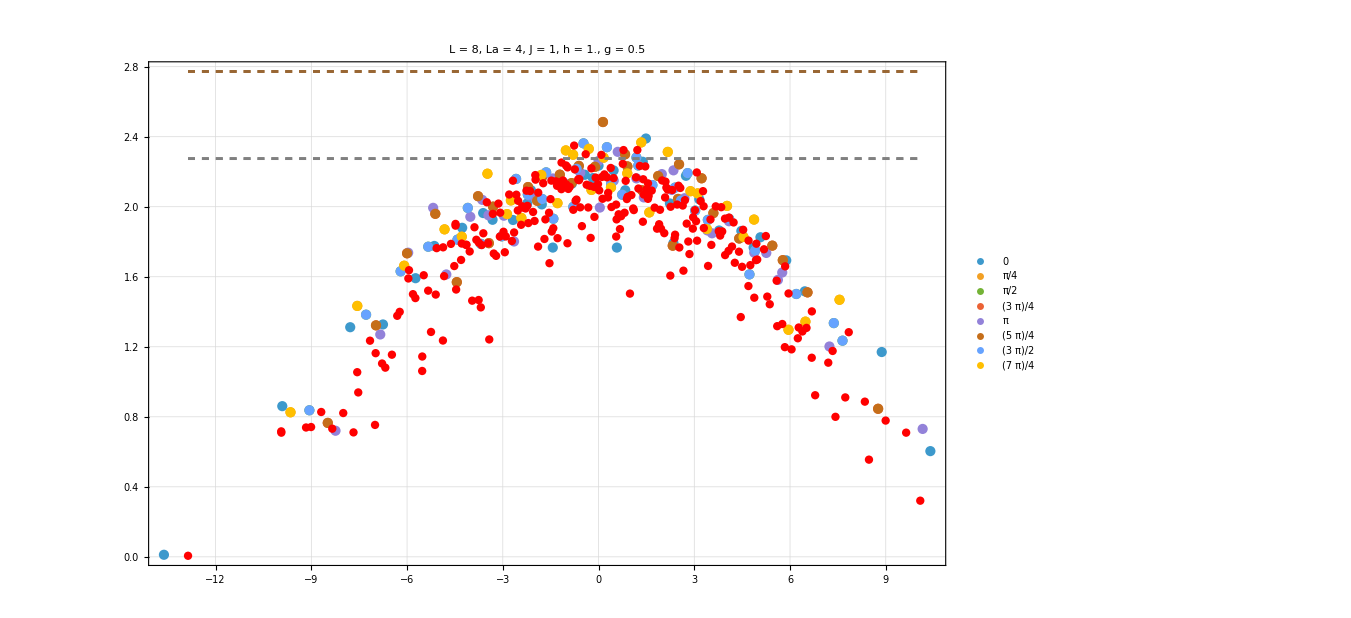

```mathematica
Show[{pbc,opc}]
```

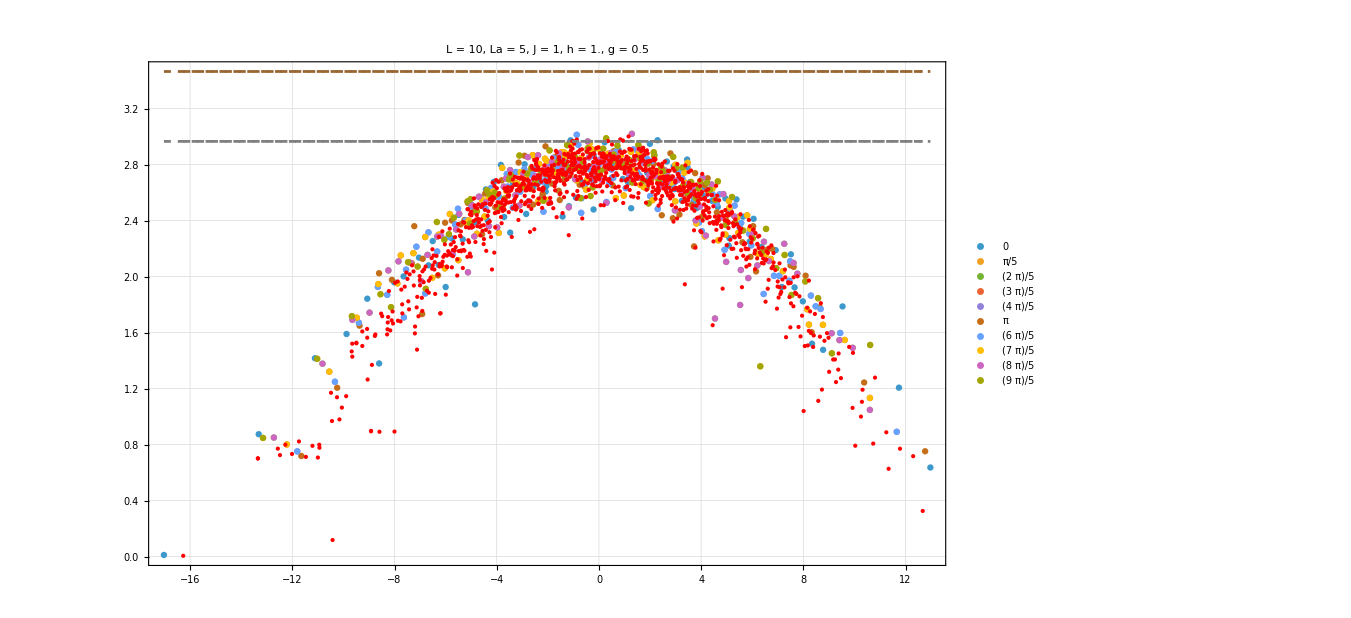

```mathematica
Show[{pbc,opc}]
```

# SVD for PBC

```mathematica
tlist=Table[10^i,{i,-1,6,0.0025}];
tlist//Length
```

2801

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,2}];
```

```mathematica
entropydata=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

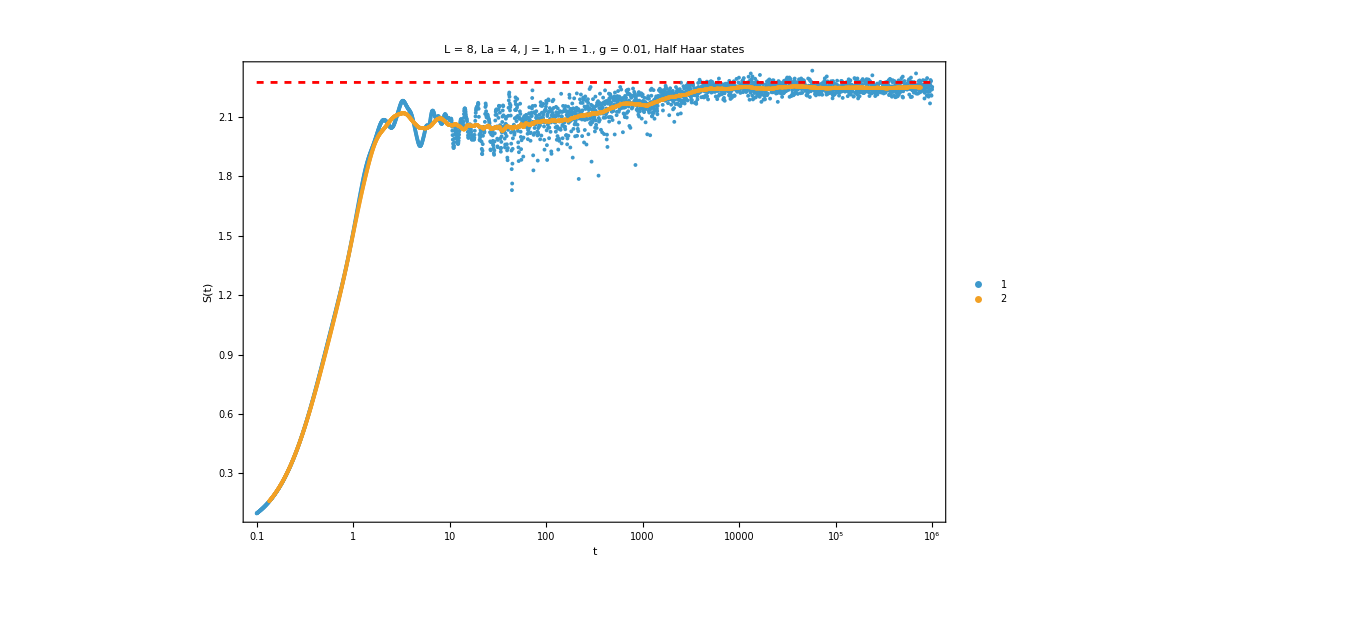

```mathematica
entropyplot=Show[{ListLogLinearPlot[{Mean[entropydata],MovingAverage[Mean[entropydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

```mathematica
Clear[schmidt];
schmidt[ini_,t_,La_,val_,vec_]:=Module[{rho,psit,ck=Conjugate[vec] . ini,a=2^(La),phases=Chop[arrayt[t,val]]*vec},
psit=N[Total[ phases*ck]];
rho=MatrixPartialTrace[Dyad[psit],2,{a,a}];
Sort[Chop[Eigenvalues[rho]]]
];
```

```mathematica
a=2^(L/2);
```

```mathematica
ini=Flatten[KroneckerProduct[haar[L/2],haar[L/2]]];
ck=Conjugate[allvecs] . ini;
phases=Chop[arrayt[1.,allvals]]*allvecs;
psit=N[Total[ phases*ck]];
rho=MatrixPartialTrace[Dyad[psit],2,{a,a}];
```

```mathematica
Sort[Chop[Eigenvalues[rho]]]
```

{5.88628×10^-6,0.0000248999,0.0000527625,0.000175309,0.000737982,0.00151405,0.00204743,0.0054521,0.00767173,0.013249,0.018831,0.0224809,0.148026,0.190665,0.243343,0.345724}

# SVD

```mathematica
tlist=Table[10^i,{i,-1,6,0.0025}];
tlist//Length
```

2801

```mathematica
productstatesfull=Table[RandomChainProductState[L],{i,2}];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,2}];
```

```mathematica
entropydata=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

```mathematica
puritydata=ParallelTable[{t,purity[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

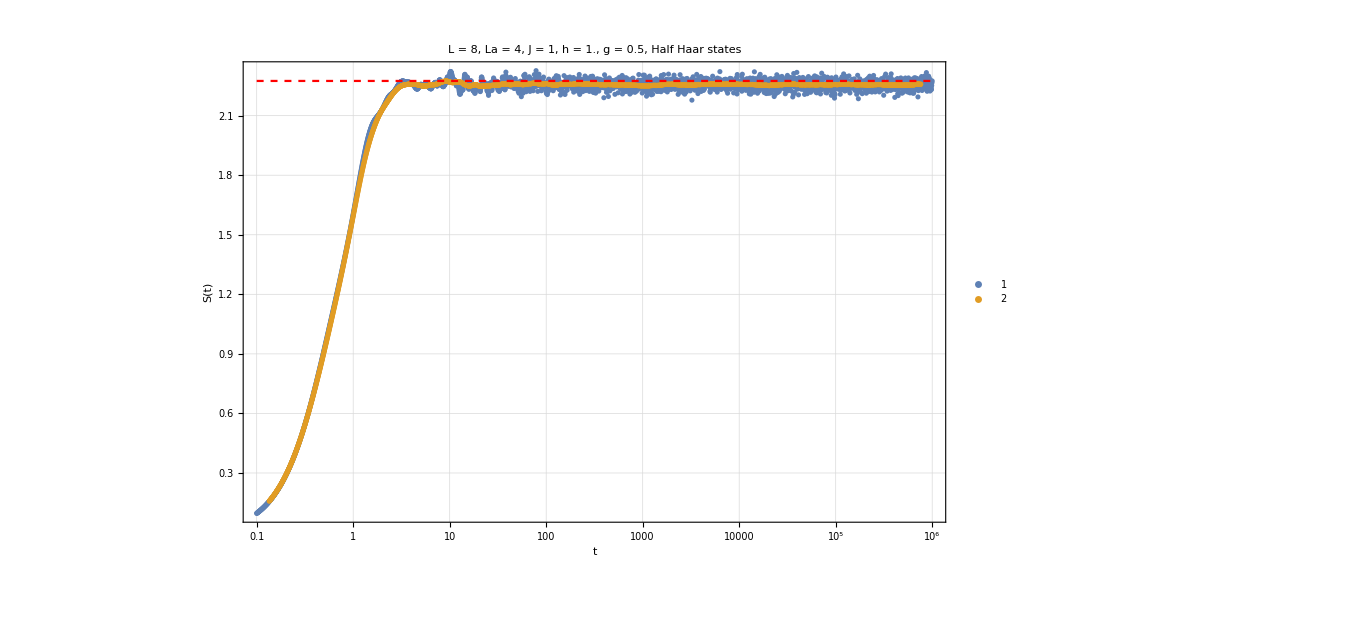

```mathematica
entropyplot=Show[{ListLogLinearPlot[{Mean[entropydata],MovingAverage[Mean[entropydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

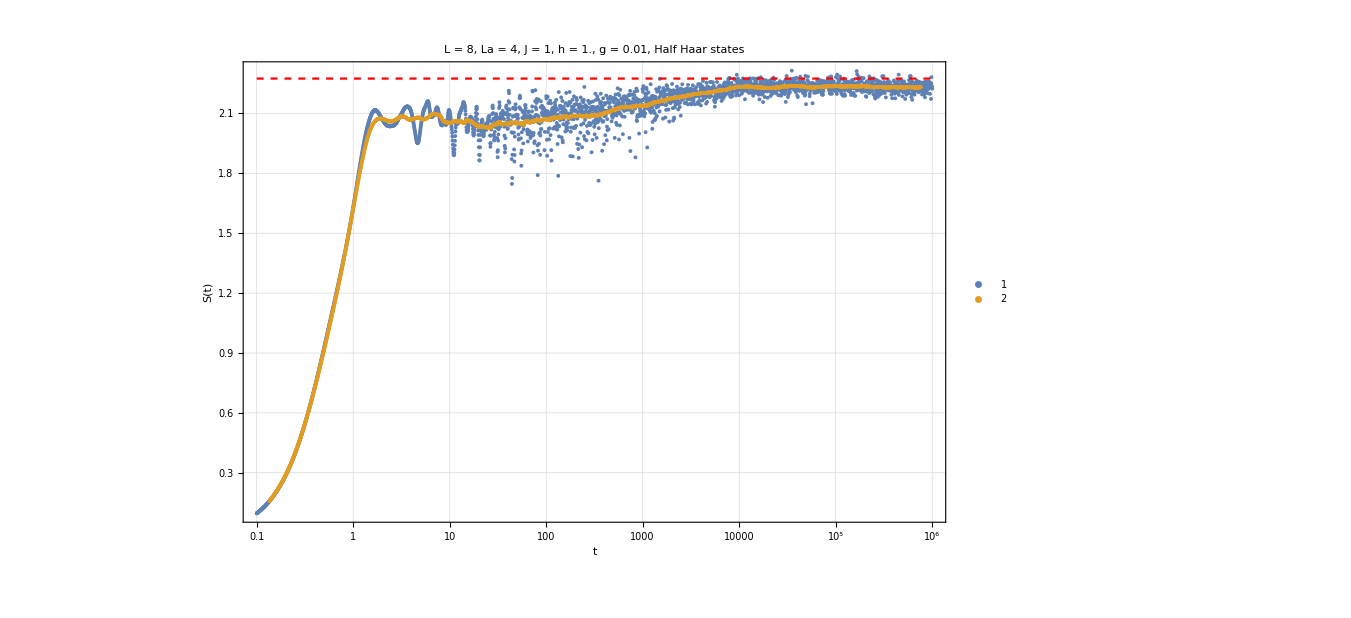

```mathematica
entropyplot=Show[{ListLogLinearPlot[{Mean[entropydata],MovingAverage[Mean[entropydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

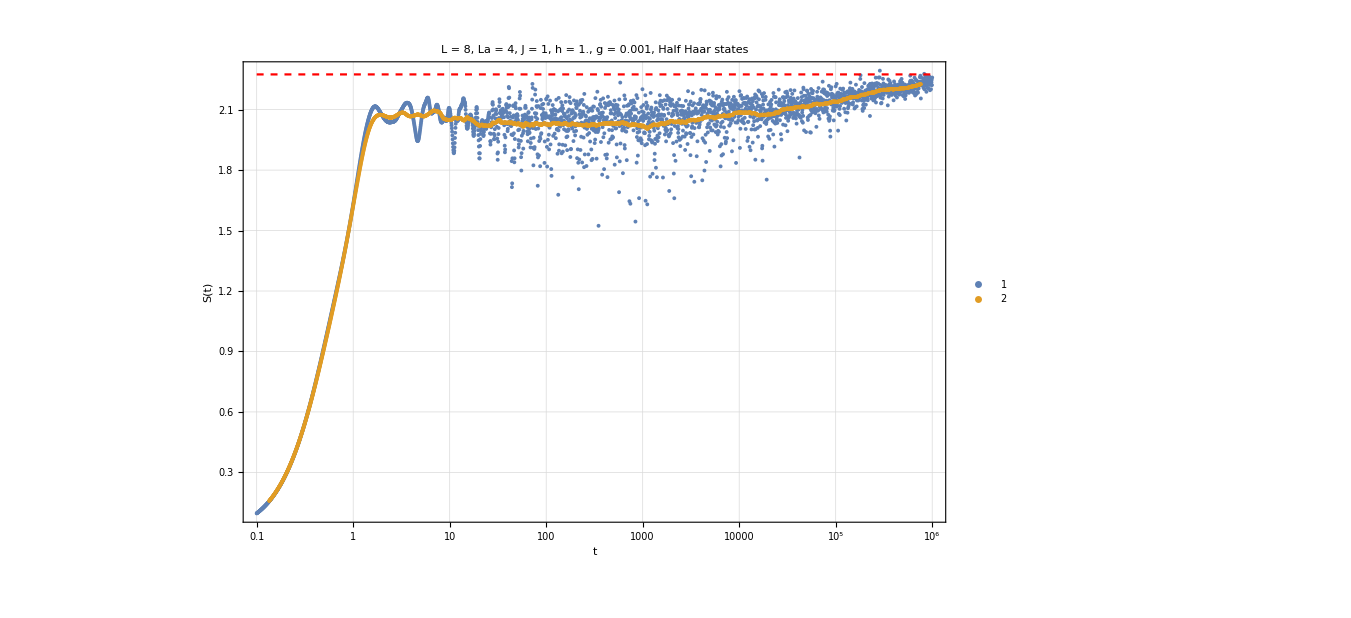

```mathematica
entropyplot=Show[{ListLogLinearPlot[{Mean[entropydata],MovingAverage[Mean[entropydata],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

## Survival probatility

```mathematica
(*productstatesfull=Table[haar[L],{i,5}];
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,5}];*)
```

```mathematica
survivaldata=ParallelTable[{t,survival[j,t,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

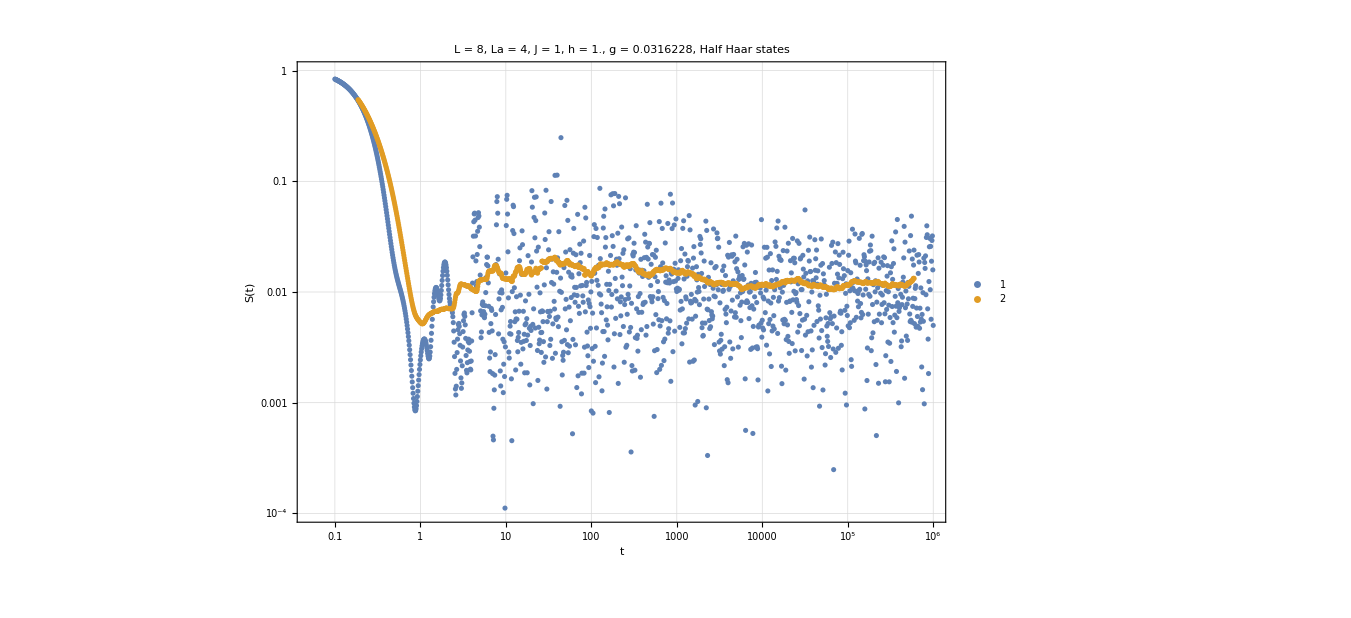

```mathematica
survivalplot=ListLogLogPlot[{Mean[survivaldata],MovingAverage[Mean[survivaldata],100]},PlotRange->{All,{10^-4,1}},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic]
```

## Spectrum

```mathematica
values=ParallelTable[schmidt[productstatesfull[[1]],t,La,allvals,allvecs],{t,tlist},DistributedContexts->Full];
```

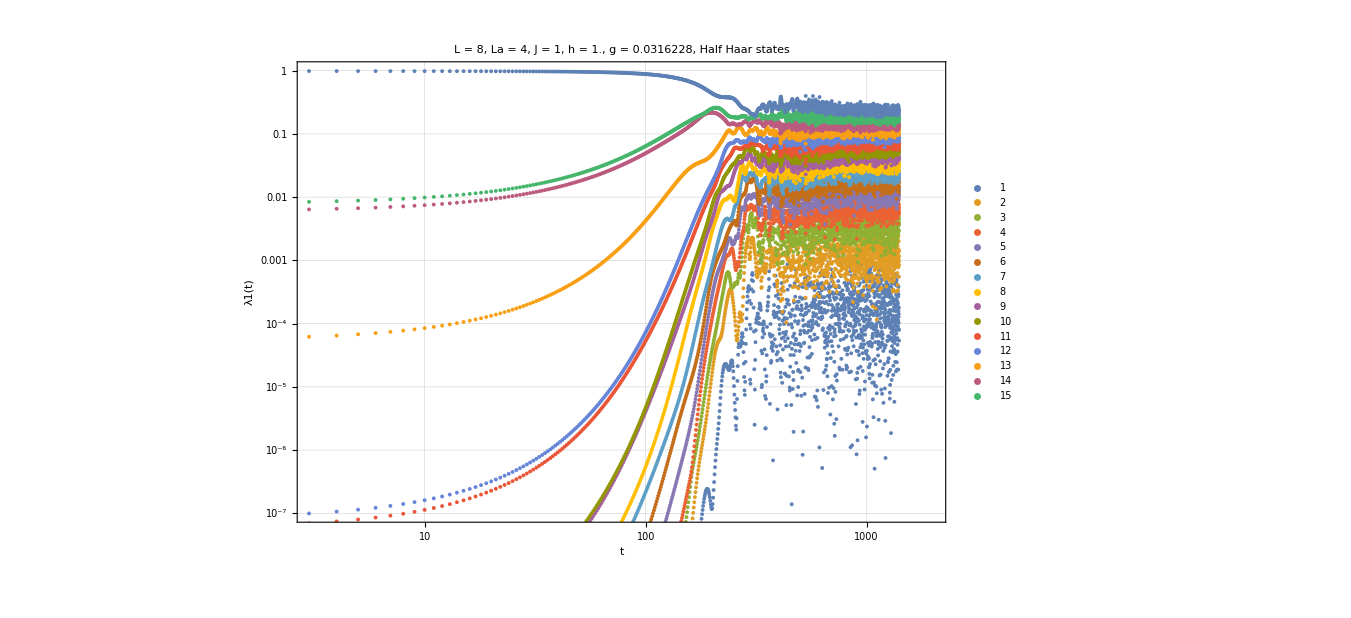

```mathematica
ListLogLogPlot[Transpose[values],Joined->False,PlotRange->{{0,2000},{10^-7,1}},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotLegends->Automatic]
```

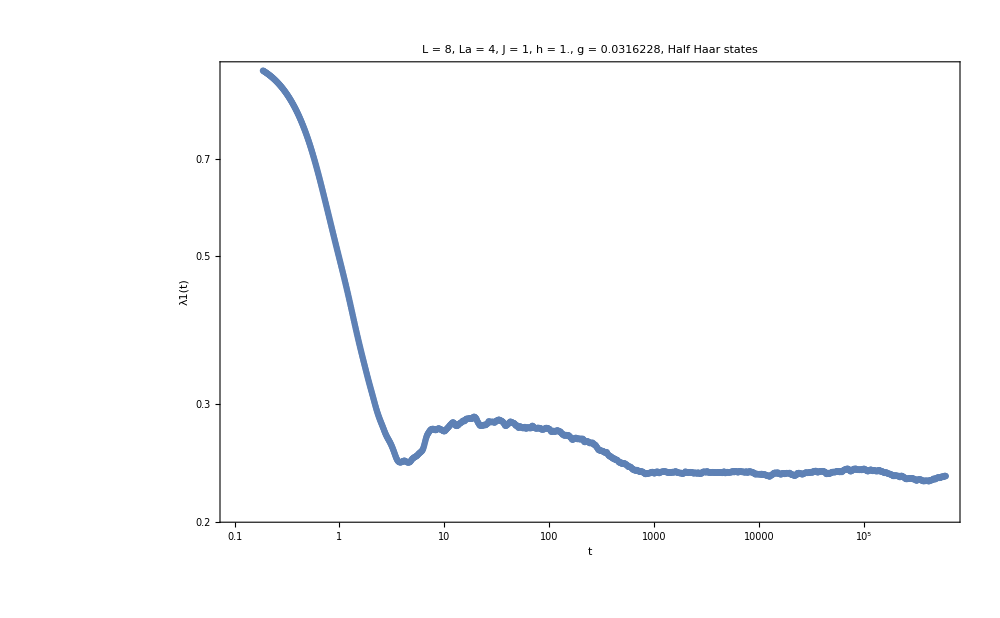

```mathematica
plot1=ListLogLogPlot[MovingAverage[Transpose[{tlist,Transpose[values][[-1]]}],100],PlotRange->All,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Half Haar states ",35,Black],FrameLabel->{Style["t",25,Black],Style["λ1(t)",25,Black]},PlotLegends->Automatic]
```

```mathematica
plots={};
```

```mathematica
AppendTo[plots,plot2];
```

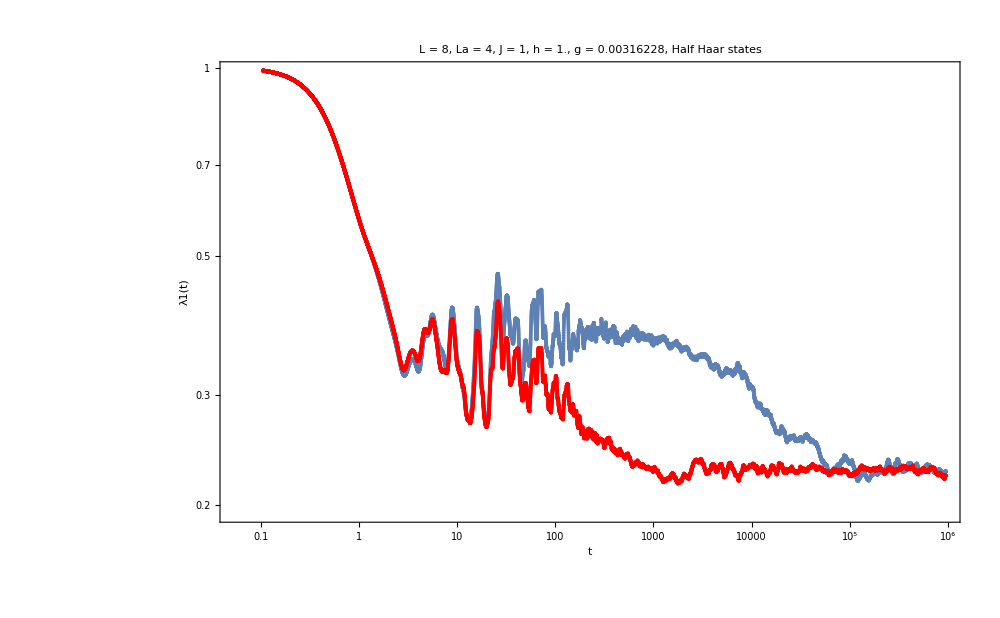

```mathematica
Show[plots]
```

# g -> 0

```mathematica
J=1;
h=1;
glist=Table[10^i,{i,-5,0.4,0.5}];
n=Length[glist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

12

```mathematica
tlist=Table[10^i,{i,-1,8,0.0025}];
tlist//Length
```

3601

```mathematica
c=N[pageEntropy[L/2,L/2]];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],10];
```

```mathematica
plots={};
alldata={};
Do[


H=IsingNNClosedHamiltonian[g,1,J,L];
{allvals,allvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{g,Length[glist]}];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>",Closed chain Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-5,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[c,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

```mathematica
Export["new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",alldata]
```

```mathematica
Export["new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

## Scaling

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_1_g.m"];
```

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
test=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 200 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-6,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[1,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["new_entanglemententropy_normalized_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

new_entanglemententropy_normalized_halfhaar_L_4_J_1_h_1_g.png

```mathematica
(*2) Nearest sample but only if within tolerance tol;otherwise Missing["NotReached",minDistance]*)
Clear[cross];
cross[data_,v_]:=Module[{vals,m,idx,tol=0.02},vals=Abs[data[[All,2]]-v];
m=Min[vals];
If[m>tol,Missing["NotReached",m],
idx=First@FirstPosition[vals,m];
data[[idx,1]]]
]
```

```mathematica
list=Table[{glist[[i]],cross[newalldata[[i]],0.9]},{i,Length[glist]}]
```

{{0.00001,238358.},{0.0000158489,149530.},{0.0000251189,87544.6},{0.0000398107,63056.4},{0.0000630957,5.68498×10^7},{0.0001,26438.},{0.000158489,6.45252×10^6},{0.000251189,2.89887×10^6},{0.000398107,1.30987×10^6},{0.000630957,467444.},{0.001,210005.},{0.00158489,1287.45},{0.00251189,29835.2},{0.00398107,578.401},{0.00630957,371.304},{0.01,239.734},{0.0158489,146.97},{0.0251189,138.749},{0.0398107,104.648},{0.0630957,26.8986},{0.1,16.0225},{0.158489,10.5252},{0.251189,4.70142},{0.398107,2.34277},{0.630957,2.04047},{1.,2.06409}}

```mathematica
Export["equilibration_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",list]
```

equilibration_entanglemententropy_halfhaar_L_4_J_1_h_1_g.m

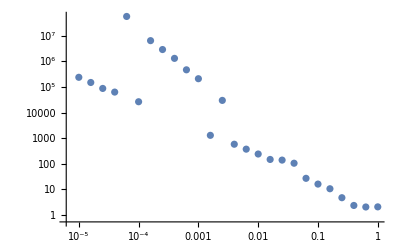

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

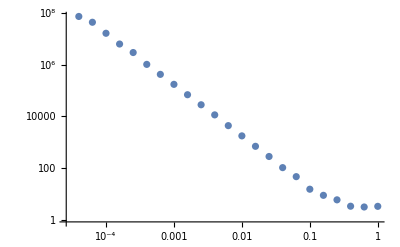

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

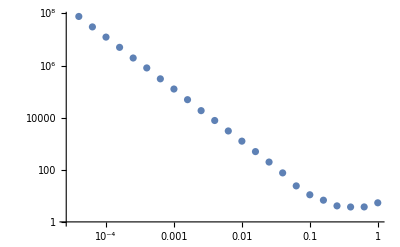

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

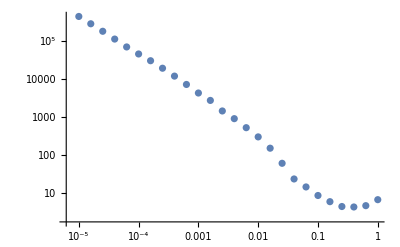

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

```mathematica
info=Table[Import["/Users/pcs/Desktop/Entropy/schmidt modes/equilibration_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_1_g.m"],{L,{4,6,8,10}}];
```

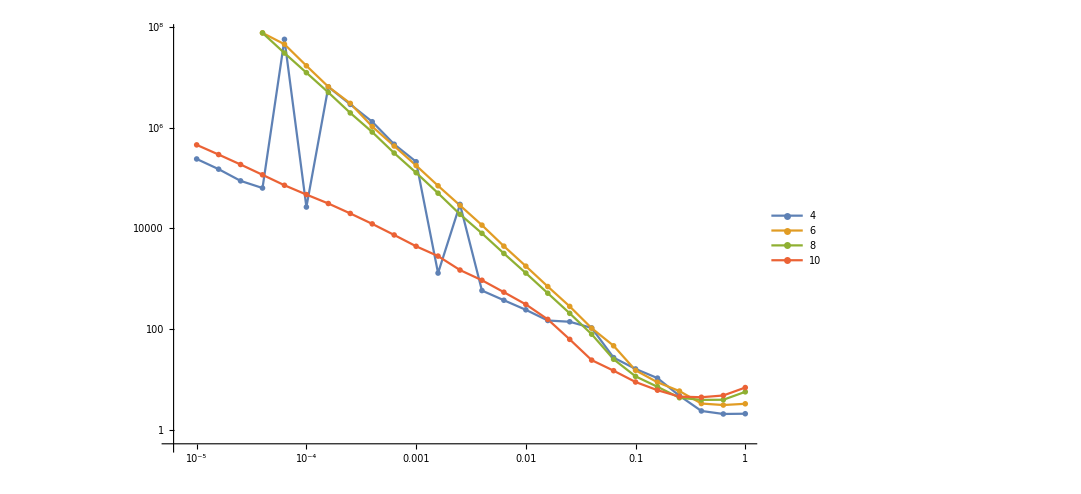

```mathematica
ListLogLogPlot[info,PlotRange->All,ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->Table[L,{L,{4,6,8,10}}]]
```

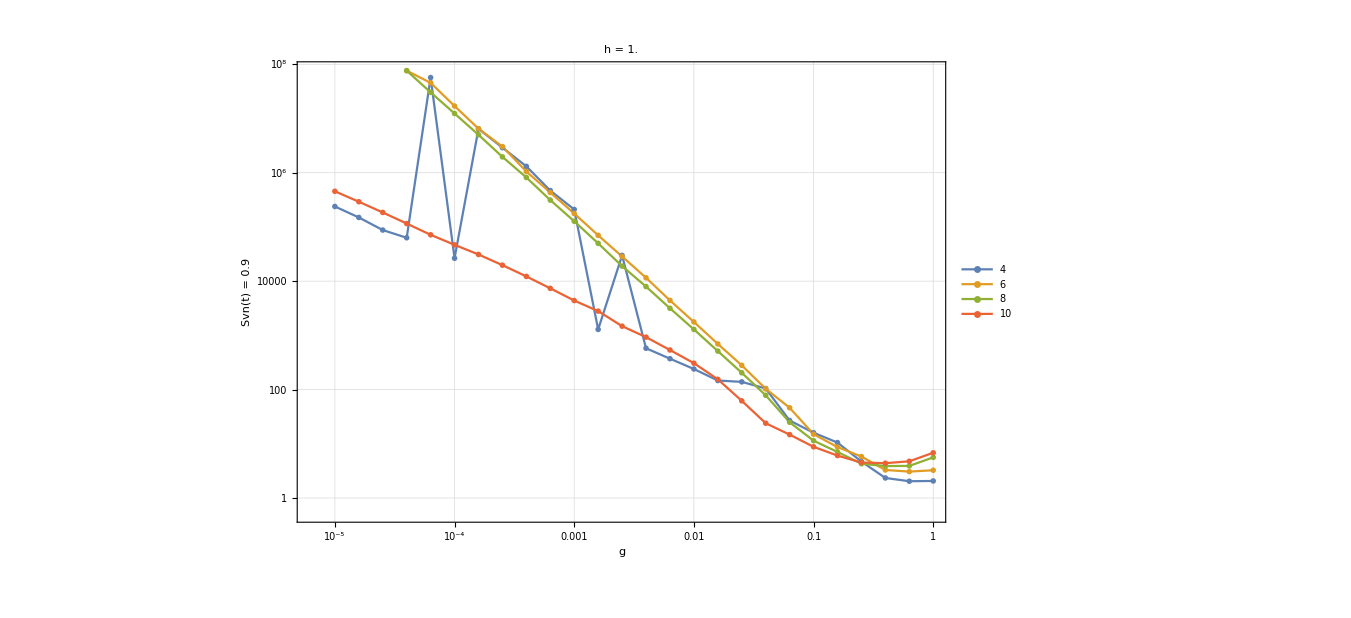

```mathematica
ListLogLogPlot[info,Joined->True,PlotMarkers->"OpenMarkers",ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["g",25,Black],Style["Svn(t) = 0.9",25,Black]},PlotRange->All,PlotLabel->Style["h = "<>ToString[N[h]]<>" ",30,Black],PlotLegends->Table[L,{L,{4,6,8,10}}]]
```